# Computation: Customer Arrivals

## by : Austin Pesina

A store opens at 8 am . From 8 am until 10 am, customers arrive at a Poisson rate of four per hour . Between 10 am and 12 pm, they arrive at a Poisson rate of eight per hour . From 12 pm to 2 pm, the arrival rate increases steadily from eight per hour at 12 pm to ten per hour at 2 pm; and from 2 pm to 5 pm, the arrival rate drops steadily from ten per hour at 2 pm to four per hour at 5 pm . Determine the probability distribution of the number of customers that enter the store on a given day .

## Abstract

In this analysis we are looking at an estimate of how many people enter a store on a given day using a Poisson distribution. By using a piecewise function using data from a given day, we can plug our function into an inhomogeneous Poisson process that gives us an estimate of 63 people entering the store on a daily basis. When we randomize data for 250 days, we still see that the mean of our distribution is around 63 people per day.

## Intensity Function

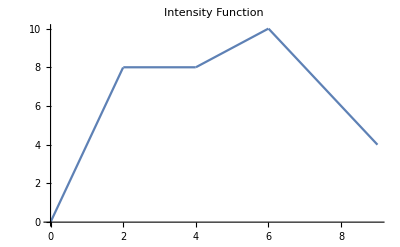

```mathematica
λ[t_]:=Piecewise[{{0+4t,0<=t<2},{8,2<=t<4}, {t+4 ,4<=t<6},{22-2t,6<=t<9}}]
Plot[λ[t],{t,0,9},PlotLabel->"Intensity Function",PlotRange->{{0,9},{0,10}}]
```

## Define the Process

```mathematica
𝒯=InhomogeneousPoissonProcess[λ[t],t]
```

InhomogeneousPoissonProcess[Piecewise[{{4 t, 0≤t<2}, {8, 2≤t<4}, {4+t, 4≤t<6}, {22-2 t, 6≤t<9}, {0, True}}],t]

```mathematica
Mean[𝒯[t]]
```

Piecewise[{{63, t>9}, {8 (-1+t), 2<t≤4}, {2 t^2, t≤2}, {-54+22 t-t^2, 6<t≤9}, {1/2 (8 t+t^2), True}}]

## Answering the Questions

(a) What is the average number of arrivals by the end of the business day?

```mathematica
Mean[𝒯[9]]
```

63

(b) What is the probability that no customers arrive before 10am?

```mathematica
PDF[PoissonDistribution[Mean[𝒯[2]]-Mean[𝒯[0]]],0]
```

ⅇ^(-8+Mean[InhomogeneousPoissonProcess[Piecewise[{{4 t, 0≤t<2}, {8, 2≤t<4}, {4+t, 4≤t<6}, {22-2 t, 6≤t<9}, {0, True}}],t][0]])

Because Mean[𝒯[0]] is not well defined, we will use a very small number that approaches 0.

```mathematica
PDF[PoissonDistribution[Mean[𝒯[2]]-Mean[𝒯[0.0001]]],0]
```

0.000335463

(c) What is the first quartile of the number of customers that arrive by the end of the business day?

```mathematica
qTable[𝒫_,t0_,tmax_,dt_,q_]:=Table[{x,InverseCDF[PoissonDistribution[(Mean[𝒫[t+1]]-Mean[𝒫[t]])],q]/.{t->x}},{x,t0,tmax,dt}];
```

```mathematica
qTable[𝒯,0.0001,9,1,0.75]
```

{{0.0001,3},{1.0001,8},{2.0001,10},{3.0001,10},{4.0001,10},{5.0001,11},{6.0001,11},{7.0001,9},{8.0001,6}}

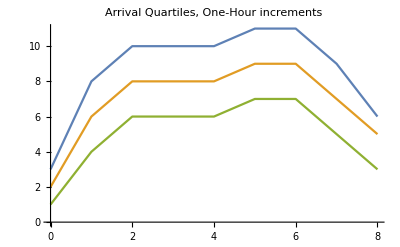

```mathematica
ListLinePlot[{qTable[𝒯,0.0001,9,1,0.75],qTable[𝒯,0.0001,9,1,0.5],qTable[𝒯,0.0001,9,1,0.25]},PlotLabel->"Arrival Quartiles, One-Hour increments"]
```

## Simulate 250 days of arrivals :

```mathematica
data=RandomFunction[𝒯,{0,9},250];
```

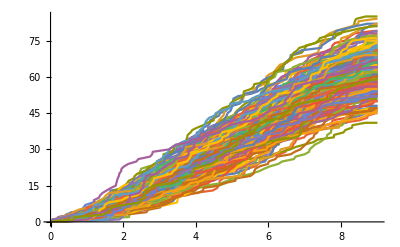

```mathematica
ListLinePlot[data,PlotRange->All]
```

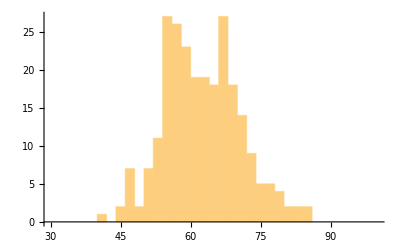

```mathematica
Histogram[data["SliceData",9],20,PlotRange->{{30,100},All}]
```

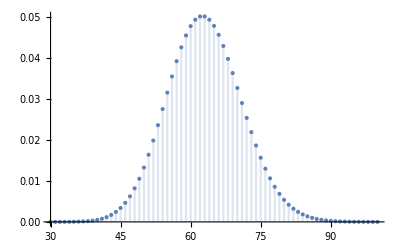

```mathematica
DiscretePlot[PDF[𝒯[9],x],{x,30,100}]
```